```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\GitHub\VM2D\settings\airfoils

```mathematica
SplitLine[a_List,b_List,h_,OptionsPattern[{FirstPoint->True,LastPoint->True}]]:=Module[{dr,np,i,j},np=Ceiling[Norm[b-a]/h];dr=(b-a)/np;(*Print[np];Print[dr];*)
i=If[OptionValue[FirstPoint],0,1];
j=If[OptionValue[LastPoint],np,np-1];
Table[a+q dr,{q,i,j}]]
```

```mathematica
(*Расширяющаяся труба - задача для внутреннего течения*)
(*pts={{6.3,0},{6.3,0.6},{-0.2,0.6},{-0.5,0.3},{-3.5,0.3},{-3.5,0},{-3.5,-0.3},{-0.5,-0.3},{-0.2,-0.6},{6.3,-0.6},{6.3,0}};
h=π/400.;*)
```

```mathematica
(*Прямоугольный профиль - из эксперимента А.Н.Нуриева*)
(*pts={{0.05,0.0},{0.05,0.5},{-0.05,0.5},{-0.05,0.0},{-0.05,-0.5},{0.05,-0.5},{0.05,0.0}};
h=0.1/20.;*)
```

```mathematica
(*Профиль с заостренными концами - из эксперимента А.Н.Нуриева*)
(*H=√(0.1^2-0.05^2)
pts={{0.05,0.0},{0.05,0.5-H},{0.0,0.5},{-0.05,0.5-H},{-0.05,0.0},{-0.05,-0.5+H},{0.0,-0.5},{0.05,-0.5+H},{0.05,0.0}};
h=0.1/20.;*)
```

```mathematica
(*Прямоугольный профиль - из эксперимента В.А.Фролова*)
(*pts={{0.25,0.0},{0.25,0.025},{-0.25,0.025},{-0.25,0.0},{-0.25,-0.025},{0.25,-0.025},{0.25,0.0}};
h=π/100.;*)
```

```mathematica
(*Тонкая пластинка - для Моргенталя*)
(*pts={{16.5,0.0},{16.5,0.165},{-16.5,0.165},{-16.5,0.0},{-16.5,-0.165},{16.5,-0.165},{16.5,0.0}};
h=0.16/8.;*)
```

```mathematica
(*Профиль моста StructureA - для Моргенталя*)
pts={{16.5,0.0},{13.3,1.425},{-13.3,1.425},{-16.5,0.0},{-13.3,-1.425},{13.3,-1.425},{16.5,0.0}};
h=0.16/(2 8.);
```

```mathematica
(*Профиль моста StructureH - для Моргенталя*)
(*pts={{6.0,0.0},{6.0,1.2},{5.6,1.2},{5.6,0.2},{-5.6,0.2},{-5.6,1.2},{-6.0,1.2},{-6.0,0.0},{-6.0,-1.2},{-5.6,-1.2},{-5.6,-0.2},{5.6,-0.2},{5.6,-1.2},{6.0,-1.2},{6.0,0.0}};
h=0.06/8.;*)
```

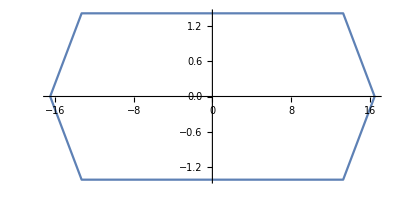

```mathematica
ListLinePlot[pts,AspectRatio->Automatic]
```

```mathematica
vertex=Flatten[Table[SplitLine[pts[[i]],pts[[i+1]],h,LastPoint->False],{i,Length@pts-1}],1];
```

```mathematica
n=Length@vertex
```

6724

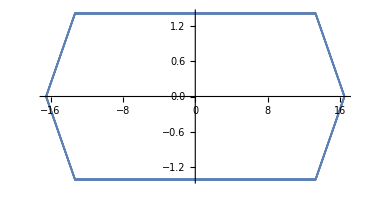

```mathematica
ListPlot[vertex,AspectRatio->Automatic]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["bridgeStructureAx2",
{"/*--------------------------------*- VM2D -*-----------------*---------------*\\
| ##  ## ##   ##  ####  #####   |                            | Version 1.10   |
| ##  ## ### ### ##  ## ##  ##  |  VM2D: Vortex Method       | 2021/05/21     |
| ##  ## ## # ##    ##  ##  ##  |  for 2D Flow Simulation    *----------------*
|  ####  ##   ##   ##   ##  ##  |  Open Source Code                           |
|   ##   ##   ## ###### #####   |  https://www.github.com/vortexmethods/VM2D  |
|                                                                             |
| Copyright (C) 2017-2021 Ilia Marchevsky, Kseniia Sokol, Evgeniya Ryatina    |
*-----------------------------------------------------------------------------*
| File name: bridgeStructureH"<>StringRepeat[" ",49]<>"|
| Info: Bridge airfoil Structure H ("<>TextString[n]<>" panels)"<>StringRepeat[" ",34-StringLength@ToString[n]]<>"|
\\*---------------------------------------------------------------------------*/ 
"}~Join~{"r = {"}
~Join~
Table[{"{",TextString@vertex[[i,1]],",",TextString@vertex[[i,2]],"},"},{i,n-1}]
~Join~
{{"{",TextString@vertex[[-1,1]],",",TextString@vertex[[-1,2]],"}"}}
~Join~
{{"};"}}
,"Table"]
```

bridgeStructureAx2